## Calculating Phase Matching Conditions; Everything starts with the Sellmeier Equations. This is for the collinear regime. Assuming monochromatic pump, uniaxial crystals and an infinitely large crystal.

Sellmeier Equations and Group Velocity Functions for BBO and YVO4

```mathematica
<<"ErrorBarPlots`"
Off[General::"spell1"]
Off[General::"spell"]
Off[General::"pspec"]
ordindex[λ_]:=√(2.7359+0.01878/(λ λ-0.01822)-0.01354 λ λ);
extindex[λ_]:=√(2.3753+0.01224/(λ λ-0.01667)-0.01516 λ λ);
airindex[λ_]:=1.000287566+1.3412/((10^18 (λ λ))/10^12);
dnodl[λ_]:=(-0.02708 λ-(0.03756 λ)/((-0.01822+λ^2)^2))/(2 √(2.7359-0.01354 λ^2+0.01878/(-0.01822+λ^2)));
dnedl[λ_]:=(-0.03032 λ-(0.02448 λ)/((-0.01667+λ^2)^2))/(2 √(2.3753-0.01516 λ^2+0.01224/(-0.01667+λ^2)));
dneffdl[λ_,θ_]:=-1/2 (-((-0.02708 λ-(0.03756 λ)/((-0.01822+λ^2)^2)) Cos[θ]^2)/((2.7359-0.01354 λ^2+0.01878/(-0.01822+λ^2))^2)-((-0.03032 λ-(0.02448 λ)/((-0.01667+λ^2)^2)) Sin[θ]^2)/((2.3753-0.01516 λ^2+0.01224/(-0.01667+λ^2))^2)) (1/(Cos[θ]^2/(2.7359-0.01354 λ^2+0.01878/(-0.01822+λ^2))+Sin[θ]^2/(2.3753-0.01516 λ^2+0.01224/(-0.01667+λ^2))))^(3/2);
yvooindex[λ_]:=Sqrt[3.77834 + 0.069736/(λ^2-0.04724)- 0.0108133λ λ];
yvoeindex[λ_]:= Sqrt[4.59905 + 0.110534/(λ^2-0.04813)-0.0122676 λ λ];
dyvooindexdl[λ_]:=(-0.0216266 λ-(0.139472 λ)/((-0.04724+λ^2)^2))/(2 √(3.77834-0.0108133 λ^2+0.069736/(-0.04724+λ^2)));

dyvoeindexdl[λ_]:=(-0.024534 λ-(0.221068 λ)/((-0.04813+λ^2)^2))/(2 √(4.59905-0.012267 λ^2+0.110534/(-0.04813+λ^2)));
C1=300000000;
bboogroupvel[λ_]:=Module[{u,no},
no=ordindex[λ];
u=1/(no - λ dnodl[λ]);
Return[C1 u];];
bboegroupvel[λ_]:=Module[{u,ne},
ne=extindex[λ];
u=1/(ne - λ dnedl[λ]);
Return[C1 u];];
ordinarygroupvel[λ_,θpm_,δ_]:=Module[{u,no},
no=ordindex[λ];
u=1/(no - λ dnodl[λ]);
Return[C1 u];];
extraordinarygroupvel[λ_,θpm_,δ_]:=Module[{u,no,ne,neff,θ},
no=ordindex[λ];ne=extindex[λ];
θ=θpm-δ;
neff=Sqrt[1/((Cos[θ]/no)^2 + (Sin[θ]/ne)^2)];
(*neff=Sqrt[1/(1/no^2 + (1/ne^2 - 1/no^2)(Sin[θ])^2)];*)
u=1/(neff - λ dneffdl[λ,θ]);
Return[C1 u];];
yvoogroupvel[λ_]:=Module[{u,no},
no=yvooindex[λ];
u=1/(no - λ dyvooindexdl[λ]);
Return[C1 u];];
yvoegroupvel[λ_]:=Module[{u,ne},
ne=yvoeindex[λ];
u=1/(ne - λ dyvoeindexdl[λ]);
Return[C1 u];];
neff[λ_,θ_]:=Module[{no,ne},
no=ordindex[λ];
ne=extindex[λ];
Return[Sqrt[1/(1/no^2 + (1/ne^2 - 1/no^2)(Sin[θ])^2)]];
];
```

```mathematica
ordindex[0.405]
neff[0.405,28.33*3.142/180]
neff[0.405,28.73*3.142/180]
```

1.69189

1.66119

1.66042

If we ignore the dispersion of the signal and idler, then the precompensation crystal that is needed is about 4.4 mm for highly nondegenerate wavelengths.

```mathematica
θ0=29π/180;δ0=0 π/180;L=15.76/1000;L1=8.2/1000;λp=0.403;λs=0.86;λi=1/(1/λp - 1/λs);π1=3.142;
Clear[ϕop,ϕep,ϕ1s,ϕ1i,ϕ2s,ϕ2i,LC];
(*After Crystal 1*)
tep = L/extraordinarygroupvel[λp,θ0,0];
top = L/ordinarygroupvel[λp,θ0,0];
tos=L/ordinarygroupvel[λs,θ0,0];
tes=L/extraordinarygroupvel[λs,θ0,0];
toi=L/ordinarygroupvel[λi,θ0,0];
tei=L/extraordinarygroupvel[λi,θ0,0];
(*Delay between SPDC photons from 1st crystal and 2nd crystal*)
(*Photons born from 1st crystal are ahead of photons in 2nd crystal*)
Δts=(top+tos)-(tos+tes)
(*Hence length of YVO4 compensator*)
LC=Δts/(1/yvoegroupvel[λp] - 1/yvoogroupvel[λp])
(*Similar analysis for idler*)
Δti=(top+toi)-(toi+tei)
LC=Δti/(1/yvoegroupvel[λp] - 1/yvoogroupvel[λp])
```

6.81997×10^-12

0.00464613

6.5118×10^-12

0.00443619

And for degenerate, we need 4.5 mm precompensator

```mathematica
(*Analysis for degenerate wavelength*)
λp=0.403;
λs=2*λp;
λi=1/(1/λp - 1/λs);
tep = L/extraordinarygroupvel[λp,θ0,0];
top = L/ordinarygroupvel[λp,θ0,0];
tos=L/ordinarygroupvel[λs,θ0,0];
tes=L/extraordinarygroupvel[λs,θ0,0];
toi=L/ordinarygroupvel[λi,θ0,0];
tei=L/extraordinarygroupvel[λi,θ0,0];
Δts=(top+tos)-(tos+tes)
LC=Δts/(1/yvoegroupvel[λp] - 1/yvoogroupvel[λp])
Δti=(top+toi)-(toi+tei)
LC=Δti/(1/yvoegroupvel[λp] - 1/yvoogroupvel[λp])
```

6.67401×10^-12

0.0045467

6.67401×10^-12

0.0045467

```mathematica
(*Dispersion Effect on Signal and Idler*)
θ0=29π/180;δ0=0 π/180;L=15.76/1000;L1=8.2/1000;λp=0.403;λs=0.85;λi=1/(1/λp - 1/λs);
tep = L/extraordinarygroupvel[λp,θ0,0];
top = L/ordinarygroupvel[λp,θ0,0];
tos=L/ordinarygroupvel[λs,θ0,0];
tes=L/extraordinarygroupvel[λs,θ0,0];
toi=L/ordinarygroupvel[λi,θ0,0];
tei=L/extraordinarygroupvel[λi,θ0,0];
Δts=top-tes;
Δti=top-tei;
Δts-Δti;

w=1/yvoegroupvel[λp]-1/yvoogroupvel[λp];
x=1/yvoogroupvel[λs]-1/yvoegroupvel[λs];
y=1/yvoogroupvel[λi]-1/yvoegroupvel[λi];
z=1/yvoegroupvel[λs]-1/yvoegroupvel[λi];

(*Post SPDC compensation crystal length*)
lac=(Δti-Δts)/-(x-y)
(*Pre Compensation crystal length*)
(Δts+lac(-x))/(1/yvoegroupvel[λp]-1/yvoogroupvel[λp])
τs
```

0.00819193

0.00903242

τs

```mathematica
tdiff[λp_,λs_]:=Module[
{λi,nop,nep,nos,nes,noi,nei,θ,td,top,tos,tes,toi,tei,lac,lpc,x,y,z,τpc,τs},
λi=(λs λp)/(λs-λp);θ=29*π/180;
nop=ordindex[λp];nep=extindex[λp];nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];
L=15.76/1000;
top = L/ordinarygroupvel[λp,θ,0];
tos=L/ordinarygroupvel[λs,θ,0];
tes=L/extraordinarygroupvel[λs,θ,0];
toi=L/ordinarygroupvel[λi,θ,0];
tei=L/extraordinarygroupvel[λi,θ,0];
Δts=top-tes;
Δti=top-tei;
Δts-Δti;
w=1/yvoegroupvel[λp]-1/yvoogroupvel[λp];
x=1/yvoogroupvel[λs]-1/yvoegroupvel[λs];
y=1/yvoogroupvel[λi]-1/yvoegroupvel[λi];
z=1/yvoegroupvel[λs]-1/yvoegroupvel[λi];

lac=0.00819193;lpc=0.00903242;
τpc=lpc w;
τs= Δts-lac x;
td=(τpc-τs)*3*10^8 * 2 π 10^6/λs;
Return[td];]

tdiffinit[i_]:=Module[
{},
λp=0.402+(i-1)*0.0001;
For[x=1,x<201,list0[[200*(i-1)+x]]=Abs[tdiff[λp,0.7+x*0.001]];x++];
Return[0];
];

list0=Table[0,{i,20*200}];
 For[index=1,index<21,tdiffinit[index];index++;];
```

```mathematica
tdiff[0.403,0.85]
```

-0.00699431

```mathematica
list1=Partition[list0,200];
Length[list1]
Length[list1[[1]]]
ListDensityPlot[list1,InterpolationOrder->1]
ListPlot3D[list1,InterpolationOrder->1]
```

20

200

-Graphics-

-Graphics3D-

```mathematica
tdiffu[λp_,λs_]:=Module[
{λi,nop,nep,nos,nes,noi,nei,θ,td,top,tos,tes,toi,tei,lac,lpc,x,y,z,τpc,τs},
λi=(λs λp)/(λs-λp);θ=29*π/180;
nop=ordindex[λp];nep=extindex[λp];nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];
L=15.76/1000;
top = L/ordinarygroupvel[λp,θ,0];
tos=L/ordinarygroupvel[λs,θ,0];
tes=L/extraordinarygroupvel[λs,θ,0];
toi=L/ordinarygroupvel[λi,θ,0];
tei=L/extraordinarygroupvel[λi,θ,0];
Δts=top-tes;
Δti=top-tei;
Δts-Δti;
w=1/yvoegroupvel[λp]-1/yvoogroupvel[λp];
x=1/yvoogroupvel[λs]-1/yvoegroupvel[λs];
y=1/yvoogroupvel[λi]-1/yvoegroupvel[λi];
z=1/yvoegroupvel[λs]-1/yvoegroupvel[λi];

lac=0.00819193;lpc=0.00903242;
τpc=lpc w;
τs= Δts-lac x;
td=(Δts)*3*10^8 * 2 π 10^6/λs;
Return[td];]

tdiffuinit[i_]:=Module[
{},
λp=0.402+(i-1)*0.0001;
For[x=1,x<201,list0[[200*(i-1)+x]]=Abs[tdiffu[λp,0.7+x*0.001]];x++];
Return[0];
];

list0=Table[0,{i,20*200}];
 For[index=1,index<21,tdiffuinit[index];index++;];
```

```mathematica
θ0=29π/180;δ0=0 π/180;L=15.76/1000;L1=8.2/1000;λp=0.4094;λs=0.85;λi=1/(1/λp - 1/λs);π1=3.142;
Clear[ϕop,ϕep,ϕ1s,ϕ1i,ϕ2s,ϕ2i,LC];
(*After Crystal 1*)
tep = L/extraordinarygroupvel[λp,θ0,0];
top = L/ordinarygroupvel[λp,θ0,0];
tos=L/ordinarygroupvel[λs,θ0,0];
tes=L/extraordinarygroupvel[λs,θ0,0];
toi=L/ordinarygroupvel[λi,θ0,0];
tei=L/extraordinarygroupvel[λi,θ0,0];
(*Delay between SPDC photons from 1st crystal and 2nd crystal*)
(*Photons born from 1st crystal are ahead of photons in 2nd crystal*)
Δts=(top+tos)-(tos+tes)
(*Hence length of YVO4 compensator*)
LC=Δts/(1/yvoegroupvel[λp] - 1/yvoogroupvel[λp])
(*Similar analysis for idler*)
Δti=(top+toi)-(toi+tei)
LC=Δti/(1/yvoegroupvel[λp] - 1/yvoogroupvel[λp])
```

6.55417×10^-12

0.00458764

6.38144×10^-12

0.00446674

```mathematica
(*Dispersion Effect on Signal and Idler*)
θ0=28.33π/180;δ0=0 π/180;L=2/1000;λp=0.4094;λs=0.735;λi=1/(1/λp - 1/λs)
tep = L/extraordinarygroupvel[λp,θ0,0];
top = L/ordinarygroupvel[λp,θ0,0];
tos=L/ordinarygroupvel[λs,θ0,0];
tes=L/extraordinarygroupvel[λs,θ0,0];
toi=L/ordinarygroupvel[λi,θ0,0];
tei=L/extraordinarygroupvel[λi,θ0,0];
Δts=top-tes;
Δti=top-tei;
Δts-Δti;

w=1/yvoegroupvel[λp]-1/yvoogroupvel[λp];
x=1/yvoogroupvel[λs]-1/yvoegroupvel[λs];
y=1/yvoogroupvel[λi]-1/yvoegroupvel[λi];
z=1/yvoegroupvel[λs]-1/yvoegroupvel[λi];

(*Post SPDC compensation crystal length*)
lac=(Δti-Δts)/-(x-y)
(*Pre Compensation crystal length*)
(Δts+lac(-x))/(1/yvoegroupvel[λp]-1/yvoogroupvel[λp])
```

0.924168

0.00103553

0.00114784

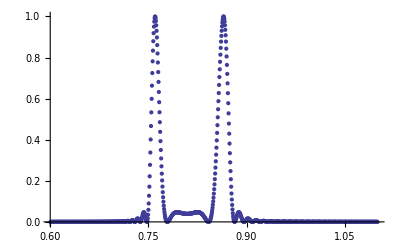

```mathematica
Clear[phasevaluelist,index];
phasematchcount[thetas_,ωp_,ωs_,ωi_,noi_,nos_,nop_,nep_, c_]:=Module[
{Θp,Θs,Θi,L,W,δkz,δky,δkx,npeff},
 Θp=28.79*π/180;
Θs=thetas*π/180;
Θi=ArcSin[nos*ωs*Sin[Θs]/(noi*ωi)];
npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];
L=6000; (*length of crystal*)
W=110;(*waist of pump *)
δkz=(npeff*ωp -nos*ωs*Cos[Θs] - noi*ωi*Cos[Θi])/(c*1000000);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);
δky=(-nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);
(*δkz=(npeff*ωp*Cos[Θp] -nos*ωs*Cos[Θp]*Cos[Θs] - noi*ωi*Cos[Θp]*Cos[Θi])/(c*1000000);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);
δky=(npeff*ωp*Sin[Θp] -nos*ωs*Sin[Θp]*Cos[Θs] - noi*ωi*Sin[Θp]*Cos[Θi])/(c*1000000);*)
Return[Exp[-W^2(δkx^2 + δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2];
];

phasevaluefinder[incre_]:=Module[
{phasevalue,λp,λs,λi,c,nop,nep,nos,nes,noi,nei,ωp,ωs,ωi,Θs,dΘs},
λp=0.4046;λs=0.6+ incre*0.0005;λi=λs*λp/(λs-λp);c=2.989*10^8;
nop=ordindex[λp];nep=extindex[λp];
nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];
ωp=2*π*c*1000000/λp;ωs=2*π*c*1000000/λs;ωi=2*π*c*1000000/λi;
       phasevalue=0;
dΘs=0.005;
       For[Θs=0,Θs<dΘs,Θs+=dΘs,phasevalue=phasematchcount[Θs,ωp,ωs,ωi,noi,nos,nop,nep,c]];
Return[phasevalue];
];
WAVELENGTHLIMIT=1000;
Clear[phasevaluelist];
phasevaluelist=Table[0,{i,WAVELENGTHLIMIT}];
For[index=1,index<WAVELENGTHLIMIT+1,index++,phasevaluelist[[index]]=phasevaluefinder[index]];
PhaseDataTable=Table[{0.6+i*0.0005,phasevaluelist[[i]]},{i,WAVELENGTHLIMIT}];
ListPlot[PhaseDataTable,PlotRange->All]
```

How about using BBO as compensators

```mathematica
(*Dispersion Effect on Signal and Idler*)
θ0=29π/180;δ0=0 π/180;L=15.76/1000;L1=8.2/1000;λp=0.403;λs=0.85;λi=1/(1/λp - 1/λs);
tep = L/extraordinarygroupvel[λp,θ0,0];
top = L/ordinarygroupvel[λp,θ0,0];
tos=L/ordinarygroupvel[λs,θ0,0];
tes=L/extraordinarygroupvel[λs,θ0,0];
toi=L/ordinarygroupvel[λi,θ0,0];
tei=L/extraordinarygroupvel[λi,θ0,0];
Δts=top-tes;
Δti=top-tei;
Δts-Δti

w=1/bboegroupvel[λp]-1/bboogroupvel[λp];
x=1/bboogroupvel[λs]-1/bboegroupvel[λs];
y=1/bboogroupvel[λi]-1/bboegroupvel[λi];
z=1/bboegroupvel[λs]-1/bboegroupvel[λi];

(*Post SPDC compensation crystal length*)
lac=(Δti-Δts)/-(x-y)
(*Pre Compensation crystal length*)
(Δts+lac(-x))/(1/bboegroupvel[λp]-1/bboogroupvel[λp])
```

2.54103×10^-13

-0.0398025

-0.0448653